# Wolfram Language Basics: Week 2 Review

## Friday, Feb 26 2021

## Requests for Review

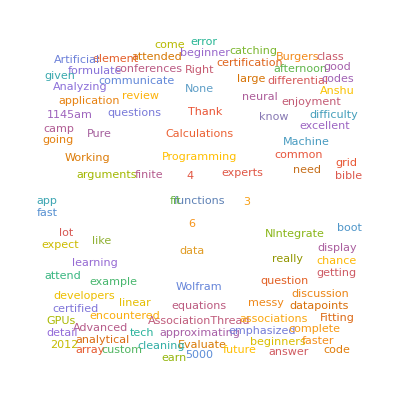

### Verbs

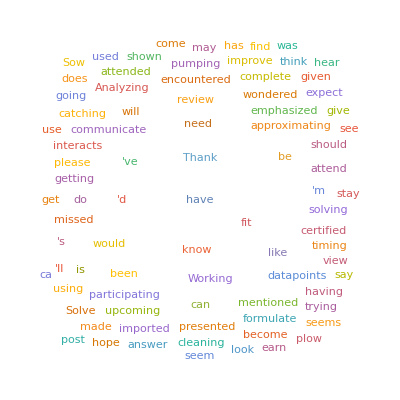

### Nouns

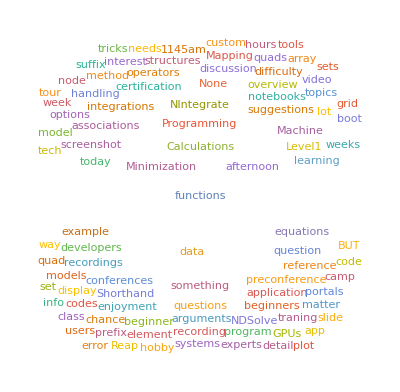

## Numerics and Symbolics

Review next Friday

## Advanced Programming and Working with Data

### Pure Functions

Pure functions, or “anonymous” functions, are functions that are introduced without being named. Pure functions are constructed using Function.

Here is a pure function that multiplies its argument by a constant:

```mathematica
Function[x,10x]
```

Pure functions are used by entering them as the head of an expression, just as other functions are used:

```mathematica
Function[x,10x][3]
```

This input represents a pure function that multiplies the argument by a constant:

```mathematica
10 #&
```

Both ways of entering the pure function have the same effect. The parentheses are not required but are included here for clarity:

```mathematica
(10 #&)[3]
```

The notation #1, #2, … can be used for pure functions with more than one argument:

```mathematica
(#1+#2 #3&)[x,y,z]
```

### Mapping Pure Functions

Pure functions are frequently used in conjunction with other functions such as Map and Apply.

This maps the pure function that squares its argument across a list:

```mathematica
Map[#^2&,{2,a,π,.001}]
```

A pure function is used here to square all those elements of a list that lie between -1 and 1:

```mathematica
Map[If[-1<#<1,#^2,#]&,{2.1,-0.25,1,-0.01,4}]
```

Pure functions are also commonly used with functions such as Select whose second argument should be a predicate function.

For example, this selects all those numbers from the list that are greater than -50:

```mathematica
Select[{100,-67,-95,-80,-22,-89,23,-19,25,100,-54,-11},#>-50&]
```

Here, the list consists of a plot of different functions:

```mathematica
TabView[
Map[Plot[#[x],{x,0,2π}]&,{Sin,Cos,Tan}]
]
```

### Pure Functions in Options for Visualizations

Since there are three variables in a surface, x, y, and z, you can give any of the three variables as arguments to the mesh, color, and region functions.

For example, this colors the surface according the third parameter, the height (#3). Try changing the #3 to #1 or #2:

```mathematica
Plot3D[E^(-x^2-y^2),{x,-2,2},{y,-2,2},ColorFunction->(Hue[#3]&)]
```

The value of the following RegionFunction option is a pure function that restricts the contour plot to the annulus defined by 1<x^2+y^2<8. Here you also specify a style for the boundary:

```mathematica
ContourPlot[x^2-y^2,{x,-π,π},{y,-π,π},RegionFunction->(1<#1^2+#2^2<8&),BoundaryStyle->{Pink,Thick}]
```

The following example gives 10 mesh lines, equally spaced on the vertical axis. Changing the MeshFunctions value from #3 to #2 will give meshes along the y axis; changing to #1 will give meshes along the x axis (#4 will give radial mesh lines):

```mathematica
ParametricPlot3D[{(3+Cos[v]) Sin[u],(3+Cos[v]) Cos[u],Sin[v]},{u,0,2π},{v,-π,π},Mesh->10,MeshFunctions->(#3&)]
```

### Short Hand Notations: Prefix and Suffix

```mathematica
words =RandomWord[10]
```

```mathematica
Map[Characters,words]
```

```mathematica
Characters/@words
```

```mathematica
StringJoin@words
```

```mathematica
words//StringJoin
```

### Thread, MapThread, AssociationThread

```mathematica
Thread[f[{a,b,c}]]
```

```mathematica
Partition[Range[9],3]
```

```mathematica
butterfly[s_String]:=StringJoin[s,StringReverse[s]]
```

```mathematica
butterfly["hello"]
```

```mathematica
butterfly[words]
```

```mathematica
Thread[butterfly[words]]
```

```mathematica
Thread[Rule[{a,b,c},{1,2,3}]]
```

```mathematica
Thread[{a,b,c}-> {1,2,3}]
```

Functions with attribute Listablepaclet:ref/Listable are threaded automatically over lists

```mathematica
Sqrt[{1,2,3,4}]
```

```mathematica
Sin[{1,2,3,4} Pi/2]
```

```mathematica
MapThread[f,{{a,b,c},{1,2,3}}]
```

```mathematica
Thread[f[{a,b,c},{1,2,3}]]
```

```mathematica
MapThread[Labeled[Framed[#1],#2]&,{{a,b,c},{1,2,3}}]
```

```mathematica
AssociationThread[{a,b,c},{1,2,3}]
```

### Evaluate and the Hold* Attributes

Nonstandard evaluation is controlled by the attributes HoldAll, HoldFirst, HoldRest, and HoldAllComplete. You can use the Attributes function to see the attributes of a symbol.

For example, NIntegrate and Plot both have the HoldAll attribute, so both functions will hold all their arguments unevaluated by default:

```mathematica
Attributes[NIntegrate]
```

```mathematica
Attributes[Plot]
```

Sometimes it is useful to force evaluation of function arguments that would otherwise have been held unevaluated. This can be done using Evaluate.

```mathematica
Plot[Normal[Series[Sin[x],{x,0,10}]],{x,-2 Pi,2 Pi}]
```

We need to force the symbolic evaluation of

```mathematica
Series[Sin[x],{x,0,someInteger}]
```

to obtain the power series expansion for Sin[x] before trying to substitute numeric values for x.

```mathematica
Plot[Evaluate[Normal[Series[Sin[x],{x,0,10}]]],{x,-2 Pi,2 Pi}]
```

### Options and Error Handling

For example, the default value for the Mesh option in Plot is None. This is the value that will be used if you do not explicitly set this optional argument:

```mathematica
Options[Plot,Mesh]
```

Setting a value for Mesh overrides the default behavior. In this case, a value of All displays all points used in the computation:

```mathematica
Plot[Sin[x+√2 Sin[x]],{x,0,2π},Mesh->All]
```

For example, the default value for the Mesh option in Plot is None. This is the value that will be used if you do not explicitly set this optional argument:

```mathematica
Options[Plot,Mesh]
```

Setting a value for Mesh overrides the default behavior. In this case, a value of All displays all points used in the computation:

```mathematica
Plot[Sin[x+√2 Sin[x]],{x,0,2π},Mesh->All]
```

#### Adding Options

You can set up any of your own functions to use optional arguments. This is accomplished by first defining option names and giving default values for these options.

For example, this defines two options, opt1 and opt2 for a function f, and gives default values:

```mathematica
Options[f]={opt1->a,opt2->b}
```

Using OptionsPattern, set up f to take optional arguments. The value of an option is extracted with OptionValue:

```mathematica
f[x_,OptionsPattern[]]:=x^2+OptionValue[opt1]/OptionValue[opt2]
```

First, try out f with one argument. In this case, the default value of the options are used:

```mathematica
f[z]
```

Explicitly setting the options causes their values to be passed and used in the body of the function:

```mathematica
f[z,opt1->α,opt2->β]
```

### Lists, Associations, Datasets

#### Lists

Lists are the most basic data structures in the Wolfram Language for easy manipulation of data.

Import the “RetailSales.tsv” data file:

```mathematica
rawData =Import["ExampleData/RetailSales.tsv","TSV"];
```

Take a peek at the data—the first few rows at the beginning of the list:

```mathematica
rawData //Shallow
```

Check how many rows and columns:

```mathematica
rawData //Dimensions
```

If there is a header row, extract it for labeling purposes later:

```mathematica
columnHeaders = First@rawData
```

Extract the data without the header rows:

```mathematica
salesData = Rest@rawData;
```

Extract specific columns of data:

```mathematica
salesByDate =salesData[[All,{1,3}]];
salesByCity =salesData[[All,{2,3}]];
```

#### Association

An Association represents data as key-value pairs.

Associations provide the dictionary data structure, where each value is labeled with and accessed by its key. This removes the need to remember separately the meaning of each entry in a list and strictly adhere to the sequence.

Here is a simple association:

```mathematica
assoc=<|a->4,b->2,c->1,d->5|>
```

You can look up a value by key:

```mathematica
assoc[b]
```

```mathematica
assoc[[2]]
```

```mathematica
assoc[[Key[b]]]
```

Many common list operations work transparently on associations:

```mathematica
Map[f,assoc]
```

```mathematica
Sort@assoc
```

```mathematica
Select[assoc,#>3&]
```

```mathematica
Total[assoc]
```

Some functions apply to keys:

```mathematica
KeyMap[f,assoc]
```

```mathematica
KeySort[assoc]
```

Extract keys or values from an association:

```mathematica
Keys[assoc]
```

```mathematica
Values[assoc]
```

Functions such as AssociationMap and AssociationThread can construct associations from lists:

```mathematica
AssociationMap[f,{a,b,c,d}]
```

```mathematica
AssociationThread[{a,b,c,d},{1,2,3,4}]
```

Associations are also returned by using functions like GroupBy, Counts, CountsBy, etc. to process data:

```mathematica
salesData =Rest[Import["ExampleData/RetailSales.tsv"]]
```

Total sales for each city:

```mathematica
GroupBy[salesData[[All,2;;3]],First-> Last, Total]
```

Number of sales for each city:

```mathematica
Counts[salesData[[All,2]]]
```

```mathematica
CountsBy[salesData,#[[2]]&]
```

#### Dataset

A Dataset is a general way of representing a hierarchy of lists and associations, constructed from tabular data.

It provides a flexible framework for sophisticated data queries and manipulations on data given a defined regular structure at arbitrary complexity:

```mathematica
d=Dataset[{
<|"a"->1,"b"->"x","c"->{1}|>,
<|"a"->2,"b"->"y","c"->{2,3}|>,
<|"a"->3,"b"->"z","c"->{3}|>,
<|"a"->4,"b"->"x","c"->{4,5}|>
}];
```

Create a Dataset from the Association created in the preceding example:

```mathematica
Dataset[salesData]
```

SemanticImport attempts to import data from a file directly into a Dataset:

```mathematica
semanticSalesData =SemanticImport["ExampleData/RetailSales.tsv"]
```

The first row in the Dataset:

```mathematica
semanticSalesData[1]
```

The element from the "City" column in the first row:

```mathematica
semanticSalesData[1,"City"]
```

Elements from all rows in the "City" column:

```mathematica
semanticSalesData[All,"City"]
```

Number of sales for each city:

```mathematica
semanticSalesData[Counts,"City"]
```

Sales that occurred before January 31, 2014:

```mathematica
semanticSalesData[Select[#Date<DateObject["Jan 31 2014"]&],{"City","Sales"}]
```

Select sales for dates prior to January 31, 2014, then group sales by city and aggregate total sales in each group:

```mathematica
semanticSalesData[Select[#Date<DateObject["Jan 31 2014"]&]/*GroupBy[#City&],Total,"Sales"]
```

### Web-scraping example

Documentation workflow

### How to look up a function for a specific task?

Navigating the documentation center

### Where to find Help?

Documentation center: Details, Examples, Tutorials

Web content:

Wolfram U: https://www.wolfram.com/wolfram-u

YouTube: https://www.youtube.com/user/WolframResearch

Twitch: https://www.twitch.tv/stephen_wolfram

Blogs:

https://writings.stephenwolfram.com/

https://blog.wolfram.com/

Technical Support

Support FAQ: https://support.wolfram.com/

Contact support: https://www.wolfram.com/support/contact/

Technical Consulting: https://www.wolfram.com/technical-consulting

Discussion forums:

Wolfram Community: https://community.wolfram.com

Stack Exchange: https://mathematica.stackexchange.com/

### Resources

#### Neural Networks and GPU processing

["http://reference.wolfram.com/language/tutorial/NeuralNetworksOverview.html"](http://reference.wolfram.com/language/tutorial/NeuralNetworksOverview.html)

["http://reference.wolfram.com/language/workflow/RunNeuralNetworkTrainingOnGPUs.html"](http://reference.wolfram.com/language/workflow/RunNeuralNetworkTrainingOnGPUs.html)

#### Working with Large Data Sets

http://reference.wolframcloud.com/language/tutorial/LoadingNumericalData.html

https://reference.wolfram.com/language/tutorial/NeuralNetworksLargeDatasets.html

Demystifying large datasets: https://www.youtube.com/watch?v=UBvjavJGWAg

## Quiz Links

https://wolfr.am/TAkF3pHi

https://wolfr.am/TAkGjQk7